```mathematica
ye=0.4295
xnuc=0.0004668
abar=28.31
zbar=ye*abar
H=8.244*10^7
rho=3.6*10^9
etae=8.154
```

0.4295

0.0004668

28.31

12.1591

8.244×10^7

3.6×10^9

8.154

```mathematica
T11=T/(10^(11))
qdotNedegen=9.2*10^(33)*T11^6*(rho/(10^(10)))
qdotNenondegen=1.1*10^(31)*etae^9*T11^9
qdot=1.769*10^(29)
tauabs=qdot*H/(1.98*10^(40)*T11^4)
rho10=rho/10^(10)
tausN=1.51729*10^(-7)*xnuc*rho10*T11^2*(1-0.112749*ye)*H
tausA=1.4578*10^(-6)*(1-xnuc)*rho10*T11^2*(abar/56*(1-1.08*zbar/abar)^2)*H
taus=tausN+tausA
tau=tauabs+taus
qdotfinal=6.62*10^(39)*T11^4/(tau/2+1/Sqrt[3]+1/(3*tauabs))/H
```

T/100000000000

3.312×10^-33 T^6

1.75279×10^-60 T^9

1.769×10^29

(7.36547×10^40)/T^4

0.36

2.00024×10^-25 T^2

6.28411×10^-22 T^2

6.28611×10^-22 T^2

(7.36547×10^40)/T^4+6.28611×10^-22 T^2

(8.03008×10^-13 T^4)/(1/(√3)+4.52562×10^-42 T^4+1/2 ((7.36547×10^40)/T^4+6.28611×10^-22 T^2))

```mathematica
qdotNedegen//.{T->8.1*10^9}
qdotNenondegen//.{T->8.1*10^9}
```

9.35407×10^26

2.63084×10^29

```mathematica
qdot
```

1.769×10^29

```mathematica
rho/mn
```

2.14935×10^33

```mathematica
qdotfinal//.{T->8.1*10^9}
```

3.76847×10^26

```mathematica
qdot
```

1.769×10^29

```mathematica
Plot[{qdot,qdotfinal},{T,10^8,10^10}]
```

-Graphics-

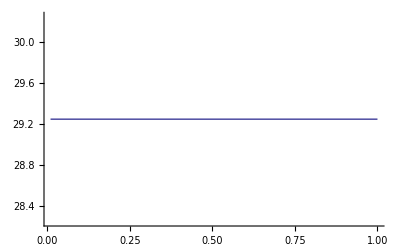

```mathematica
Plot[Log[10,qdot],{T,10^8,10^10}]
```

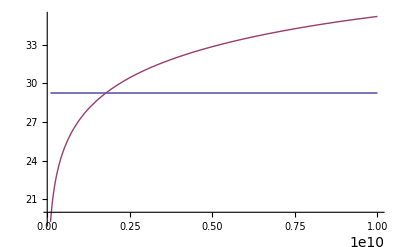

```mathematica
Plot[{Log[10,qdot],Log[10,qdotfinal]},{T,10^8,10^10}]
```

```mathematica
tauabsdim02=4.5*10^(-7)*T11^2*xnuc*rho10*H
tauabsdim02//.{T->8.1*10^9}
```

6.23424×10^-25 T^2

0.0000409029

```mathematica
tauabsdim02=qdot*H/(4*(7/8)*sigmasb*T^4)
tauabsdim02//.{T->8.1*10^9}
```

(7.34722×10^40)/T^4

17.068

```mathematica
tauabs//.{T->8.1*10^9}
```

17.1104

```mathematica
taus//.{T->8.1*10^9}
```

0.0412432

```mathematica
tausN//.{T->8.1*10^9}
tausA//.{T->8.1*10^9}
```

0.0000131236

0.0412301

```mathematica
tau//.{T->8.1*10^9}
```

0.11859

```mathematica
rho10
```

0.36

```mathematica
T10=T11
```

T10